Vspec = 14.0446

Pspec = abc = 3.3529

N = 600

λ1 = 5.30468   λN = 207.869

Fw min/max: {-5.11377,3.93388}

S(L) min/max: {0.187171,34298.2}

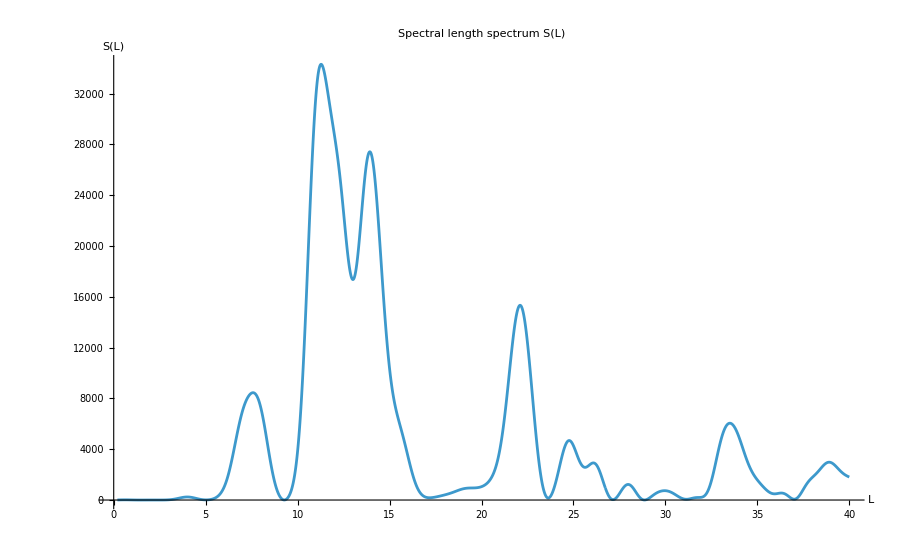

#topPeaks = 14

Top 12 peaks (L,S):

11.281 | 34298.2
13.9277 | 27410.7
22.1 | 15327.8
7.57627 | 8448.18
33.506 | 6046.32
24.7666 | 4682.74
38.9055 | 2977.37
26.0833 | 2920.73
27.9738 | 1226.17
29.9571 | 735.376
36.3019 | 549.761
4.0009 | 239.719

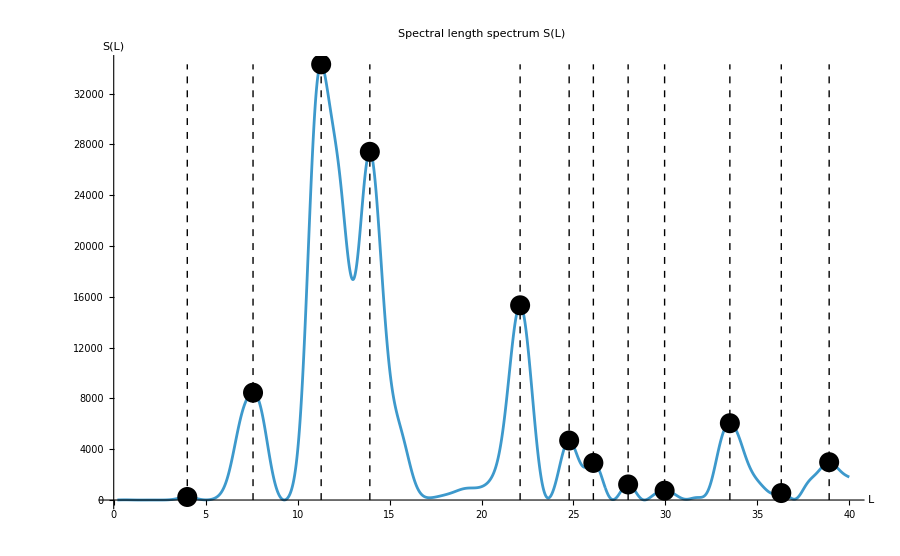

Lpool size = 6

Lpool sample: {0.6179,2.14025,4.0009,7.57627,11.281,13.9277}

Top 10 clusters (size, centroid):

7010 | 0.528439
1.8499
3.42998
6884 | 0.797741
1.50115
2.79999
3579 | 0.856337
1.62159
2.41454
3514 | 0.698149
1.30509
3.67986
3510 | 1.06996
1.59316
1.96694
3506 | 0.650785
1.21655
4.23499
3461 | 0.699042
1.97103
2.43346
3455 | 0.460654
2.42805
2.99771
3447 | 0.564307
1.99759
2.97439

BEST centroid (Route 3 fixed) = {0.528439,1.8499,3.42998}

#supporting triples = 7010

Top 20 supporting L-triples:

0.6179 | 4.0009 | 7.57627
0.6179 | 7.57627 | 11.281
2.14025 | 4.0009 | 13.9277
0.6179 | 4.0009 | 7.57627
0.6179 | 4.0009 | 11.281
0.6179 | 7.57627 | 13.9277
2.14025 | 4.0009 | 7.57627
0.6179 | 4.0009 | 7.57627
2.14025 | 4.0009 | 11.281
0.6179 | 11.281 | 13.9277
0.6179 | 2.14025 | 4.0009
4.0009 | 7.57627 | 11.281
0.6179 | 2.14025 | 4.0009
2.14025 | 4.0009 | 7.57627
0.6179 | 7.57627 | 11.281
2.14025 | 11.281 | 13.9277
7.57627 | 11.281 | 13.9277
0.6179 | 4.0009 | 13.9277
2.14025 | 7.57627 | 11.281
2.14025 | 4.0009 | 13.9277

#supporting triples = 7010

Top 20 supporting L-triples:

0.6179 | 4.0009 | 7.57627
0.6179 | 7.57627 | 11.281
2.14025 | 4.0009 | 13.9277
0.6179 | 4.0009 | 7.57627
0.6179 | 4.0009 | 11.281
0.6179 | 7.57627 | 13.9277
2.14025 | 4.0009 | 7.57627
0.6179 | 4.0009 | 7.57627
2.14025 | 4.0009 | 11.281
0.6179 | 11.281 | 13.9277
0.6179 | 2.14025 | 4.0009
4.0009 | 7.57627 | 11.281
0.6179 | 2.14025 | 4.0009
2.14025 | 4.0009 | 7.57627
0.6179 | 7.57627 | 11.281
2.14025 | 11.281 | 13.9277
7.57627 | 11.281 | 13.9277
0.6179 | 4.0009 | 13.9277
2.14025 | 7.57627 | 11.281
2.14025 | 4.0009 | 13.9277

Top 15 La by microlocal sparsity score:

2.14025 | 0.406155
4.0009 | 0.389943
7.57627 | 0.375269

Chosen bestLa = 2.14025  score=0.406155

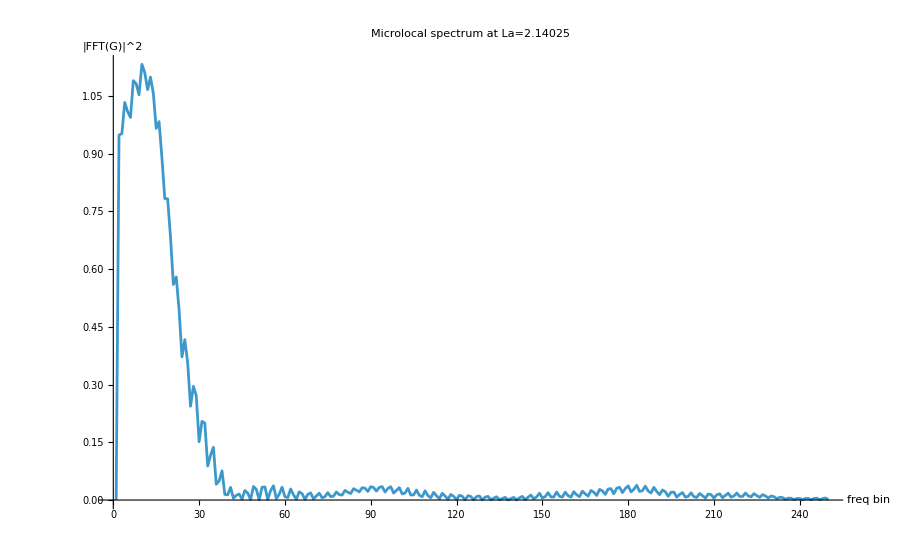

Top 20 microlocal candidates: {L, Q, coherence, peakiness}

4.0009 | 0.030301 | 0.0870491 | 0.348091
2.1402 | 0.0249395 | 0.0700683 | 0.355931
7.5763 | 0.0204852 | 0.0583603 | 0.351013

Chosen microlocal L's = {2.1402,4.0009,7.5763}

Axes from microlocal-selected L's = {0.797208,1.4903,2.82211}

Top10 microlocal L's: {4.0009,2.1402,7.5763}

Best triples by |alpha-2| (then microlocal strength):

{{2.140200,4.000900,7.576300},2.684620,0.684620,1.315380,{0.797208,1.490304,2.822112},14.044594,0.000015}

Best triples by |alpha-4| (then microlocal strength):

{{2.140200,4.000900,7.576300},2.684620,0.684620,1.315380,{0.797208,1.490304,2.822112},14.044594,0.000015}

```mathematica
(* ============================================================Route 3.bd (DeepMath):Weyl volume+length-spectrum ensemble+microlocal (orbit-local) frequency extraction (qBNF-flavor)============================================================*)
Clear["Global`*"];

(*-----------------------0) INPUTS-----------------------*)
eigenvalueFilePath="C:\\Users\\sulta\\git\\cone-operator-lab\\data\\eigenvalues\\ellipsoid_eigs_a1_b1.5_c2.3_arnoldi-1000.txt";
eigsIndexRange={1,600};

(*Weyl fit coefficients (numeric!)*)
A0fit=N@0.2371691511;
A1fit=N@(-0.5401975968);
A2fit=N@0.03937795600473376;

(*length spectrum grid*)
Lmin=0.2;Lmax=40.0;nL=12000;

(*precision for exp(-i L t)*)
wp=50;

(*peak/ensemble parameters*)
topM=200;        (*keep this many peaks (by height)*)
useMpeaks=80;    (*use first M peak locations for triple building*)
sampleN=50000;   (*weighted triple sampling size*)
clusterEps=0.07; (*cluster proximity threshold for supporting triples*)

(*microlocal parameters*)
sigmaPhase=0.25;      (*phase-window width (smaller->more localized)*)
nFreqPlot=250;        (*show first nFreqPlot bins in transverse spectrum*)

(*-----------------------1) WEYL+HARD VOLUME-----------------------*)
Vspec=6 Pi^2 A0fit;
Pspec=(3 Vspec)/(4 Pi);  (*abc*)

Print["Vspec = ",N@Vspec];
Print["Pspec = abc = ",N@Pspec];

Nweyl[λ_?NumericQ]:=A0fit*λ^(3/2)+A1fit*λ+A2fit*Sqrt[λ];

scaleAxesFromL[L_List]:=Module[{s},s=(Pspec/(Times@@L))^(1/3);
Sort[s L]];

(*-----------------------2) LOAD EIGENVALUES-----------------------*)
raw=Import[eigenvalueFilePath,"Table"]//Flatten;
lam=Sort[raw][[eigsIndexRange[[1]];;eigsIndexRange[[2]]]]//N;
Nvals=Length[lam];

Print["N = ",Nvals];
Print["λ1 = ",First[lam],"   λN = ",Last[lam]];

k=N@Range[Nvals];
t=Sqrt[lam];
F=k-(Nweyl/@lam);

(*Hann window*)
w=N@Table[0.5 (1-Cos[2 Pi (j-1)/(Nvals-1)]),{j,1,Nvals}];
Fw=F*w;

Print["Fw min/max: ",{Min[Fw],Max[Fw]}];

(*-----------------------3) LENGTH SPECTRUM S(L)-----------------------*)
Lgrid=Subdivide[Lmin,Lmax,nL];

Svals=Table[Abs[Total[SetPrecision[Fw,wp]*Exp[-I*SetPrecision[L,wp]*SetPrecision[t,wp]]]]^2,{L,Lgrid}]//N;

Print["S(L) min/max: ",{Min[Svals],Max[Svals]}];

basePlot=ListLinePlot[Transpose[{Lgrid,Svals}],PlotRange->All,AxesLabel->{"L","S(L)"},ImageSize->900,PlotLabel->"Spectral length spectrum S(L)"];

basePlot

(*-----------------------4) PEAK EXTRACTION-----------------------*)
localMaximaIdx[y_List]:=Flatten@Position[Table[1<i<Length[y]&&y[[i]]>y[[i-1]]&&y[[i]]>y[[i+1]],{i,1,Length[y]}],True];

topPeaksFromLS[Lg_List,Sv_List,M_:200]:=Module[{idx,peaks,sorted},idx=localMaximaIdx[Sv];
peaks={Lg[[#]],Sv[[#]]}&/@idx;
sorted=Reverse@SortBy[peaks,Last];
Take[sorted,UpTo[Min[M,Length[sorted]]]]];

topPeaks=topPeaksFromLS[Lgrid,Svals,topM];
Print["#topPeaks = ",Length[topPeaks]];
Print["Top 12 peaks (L,S):"];
Print[Take[topPeaks,UpTo[12]]//TableForm];

(*highlight the 12 strongest peaks*)
peakMarks=topPeaks[[;;Min[12,Length[topPeaks]]]][[All,1]];
plotPeaks12=Show[basePlot,Graphics[{PointSize[0.016],Table[Module[{idx=First@Ordering[Abs[Lgrid-L0],1]},{Point[{Lgrid[[idx]],Svals[[idx]]}],Dashed,Line[{{L0,0},{L0,Max[Svals]}}]}],{L0,peakMarks}]}]];
plotPeaks12

(*-----------------------5) ROUTE 3: helpers:peak strength near L-----------------------*)
(*---start from your extracted peaks---*)peakL=topPeaks[[All,1]];
peakS=topPeaks[[All,2]];

nearestStrength[L_?NumericQ,relTol_:0.02]:=Module[{idx,tol},tol=relTol*L;
idx=First@Ordering[Abs[peakL-L],1];
If[Abs[peakL[[idx]]-L]<=tol,peakS[[idx]],0.0]];

(*primitive filter:remove L if it is close to m*Lsmall for some smaller peak*)
isMultipleOfSmaller[L_?NumericQ,relTol_:0.02,mMax_:8]:=Module[{smaller,m,hit},smaller=Select[peakL,#<L&];
hit=False;
Do[If[AnyTrue[smaller,Abs[L-m #]<=relTol*L&],hit=True;Break[]],{m,2,mMax}];
hit];

(*build pool:take strongest peaks but keep only "primitive" ones,prefer short L*)
rawPool=Take[peakL,UpTo[150]];

Lpool=Select[rawPool,(#<12.0)&&(!isMultipleOfSmaller[#,0.025,10])&];

(*fallback if too small*)
If[Length[Lpool]<12,Lpool=Union[Lpool,Select[peakL,#<15.0&]]];

Lpool=Take[DeleteDuplicates[Lpool],UpTo[80]];
Spool=(nearestStrength[#,0.03]&/@Lpool);
wpool=Spool/Total[Spool];

Print["Lpool size = ",Length[Lpool]];
Print["Lpool sample: ",Take[Lpool,UpTo[20]]];

(*---------CRUCIAL FIX:sample 3 DISTINCT L's (no duplicates)---------*)
sampleDistinctTriple[]:=Sort@RandomSample[Lpool,3];

triplesSamp=Table[sampleDistinctTriple[],{70000}];
axesSamp=scaleAxesFromL/@triplesSamp;

axesSamp=Select[axesSamp,(#[[1]]>0.2&&#[[3]]<10&&#[[3]]/#[[1]]<10)&];

clusters=FindClusters[axesSamp,DistanceFunction->EuclideanDistance];
centroids=Mean/@clusters;
sizes=Length/@clusters;

summary=Reverse@SortBy[Transpose[{sizes,centroids}],First];
Print["Top 10 clusters (size, centroid):"];
Print[Take[summary,UpTo[10]]//TableForm];

bestCentroid=First[summary][[2]];
Print["BEST centroid (Route 3 fixed) = ",N@bestCentroid];




epsAxes=0.06;
goodIdx=Flatten@Position[Map[Norm[#-bestCentroid]<epsAxes&,axesSamp],True];
goodTriples=triplesSamp[[goodIdx]];

Print["#supporting triples = ",Length[goodTriples]];
Print["Top 20 supporting L-triples:"];
Print[Take[goodTriples,UpTo[20]]//TableForm];




epsAxes=0.06;
goodIdx=Flatten@Position[Map[Norm[#-bestCentroid]<epsAxes&,axesSamp],True];
goodTriples=triplesSamp[[goodIdx]];

Print["#supporting triples = ",Length[goodTriples]];
Print["Top 20 supporting L-triples:"];
Print[Take[goodTriples,UpTo[20]]//TableForm];



(*----------microlocal scoring for a list of candidate La----------*)wrapToPi[x_]:=Mod[x+Pi,2 Pi]-Pi;

orbitWeightVec[L0_?NumericQ,sig_?NumericQ]:=Exp[-(wrapToPi[t*L0]^2)/(2 sig^2)];

microlocalSpectrum[L0_?NumericQ,sig_?NumericQ]:=Module[{wL,G,Spec},wL=orbitWeightVec[L0,sig];
G=(Fw*wL);
G=G-Mean[G];
Spec=Abs[Fourier[G]]^2;
Spec];

(*score:how "peaky" the transverse spectrum is (2-dof->a few dominant bins)*)
microlocalScore[L0_?NumericQ,sig_?NumericQ,kmax_:250]:=Module[{Spec,band,s1,sTot,sparsity},Spec=microlocalSpectrum[L0,sig];
band=Take[Spec,kmax];
(*ignore DC*)band[[1]]=0;
sTot=Total[band]+10^-12;
s1=Total[Take[Reverse@Sort[band],10]];(*energy in top 10 bins*)sparsity=s1/sTot;(*closer to 1=>few strong lines*)N@sparsity];

(*candidate La:take short peaks only*)
candLa=Select[topPeaks[[All,1]],1.5<=#<=9.5&]//DeleteDuplicates;

sig=0.22;
scoresLa=Table[{L0,microlocalScore[L0,sig,250]},{L0,candLa}];
scoresLaSorted=Reverse@SortBy[scoresLa,Last];

Print["Top 15 La by microlocal sparsity score:"];
Print[Take[scoresLaSorted,UpTo[15]]//TableForm];

bestLa=First[scoresLaSorted][[1]];
Print["Chosen bestLa = ",N@bestLa,"  score=",First[scoresLaSorted][[2]]];

(*visualize best La microlocal spectrum*)
SpecBest=microlocalSpectrum[bestLa,sig];
ListLinePlot[Take[SpecBest,250],PlotRange->All,AxesLabel->{"freq bin","|FFT(G)|^2"},ImageSize->900,PlotLabel->Row[{"Microlocal spectrum at La=",NumberForm[bestLa,6]}]]




Lpool=Take[scoresLaSorted[[All,1]],UpTo[30]];






(*-----------------------------Microlocal quality score Q(L)-----------------------------*)wrapToPi[x_]:=Mod[x+Pi,2 Pi]-Pi;

orbitWeightVec[L0_?NumericQ,sig_?NumericQ]:=Exp[-(wrapToPi[t*L0]^2)/(2 sig^2)];

microlocalScore[L0_?NumericQ,sig_:0.25,wp_:50,nBins_:200]:=Module[{wL,G,G0,coh,Spec,peakiness,top},wL=orbitWeightVec[L0,sig];
G=SetPrecision[Fw,wp]*SetPrecision[wL,wp];
(*coherence:how much energy survives the microlocal window*)coh=(Norm[G]^2)/(Norm[Fw]^2+10^-30);
(*transverse spectrum peakiness*)G0=G-Mean[G];
Spec=Abs[Fourier[G0]]^2//N;
Spec=Take[Spec,UpTo[nBins]];
top=Take[Reverse@Sort[Spec[[2;;]]],UpTo[8]];(*ignore DC*)peakiness=(Total[top])/(Total[Spec]+10^-30);
(*combined score:coherence*peakiness*){coh*peakiness,coh,peakiness}];

(*evaluate Q on candidate peak lengths (short regime)*)
candL=Select[topPeaks[[All,1]],1.0<=#<=10.0&];   (*start broad*)
candL=DeleteDuplicates[Round[candL,0.0001]];

scoresL=Table[With[{res=microlocalScore[L,0.25,50,220]},{L,res[[1]],res[[2]],res[[3]]}],{L,candL}];

scoresL=Reverse@SortBy[scoresL,#[[2]]&];

Print["Top 20 microlocal candidates: {L, Q, coherence, peakiness}"];
Print[Take[scoresL,UpTo[20]]//TableForm];




(*choose 3 microlocal winners,separated in L*)chosenL={};
Do[If[Length[chosenL]<3&&AllTrue[chosenL,Abs[#-scoresL[[i,1]]]>0.6&],AppendTo[chosenL,scoresL[[i,1]]]],{i,1,Length[scoresL]}];

chosenL=Sort[chosenL];
Print["Chosen microlocal L's = ",chosenL];

axesMicro=scaleAxesFromL[chosenL];
Print["Axes from microlocal-selected L's = ",axesMicro];



(*----------prerequisites---------- You already have:-scoresL={{L,Q,coherence,peakiness},...} sorted descending by Q-A0fit numeric*)(*---spectral volume from A0fit---*)Vspec=6 Pi^2 A0fit;

(*helper:alpha inferred from volume if L≈alpha*a=>a≈L/alpha*)
alphaFromTriple[L_List,V_?NumericQ]:=Module[{prodL},prodL=Times@@L;
(*V=(4π/3) (L1/α)(L2/α)(L3/α)=(4π/3) prodL/α^3*)((4 Pi/3) prodL/V)^(1/3)];

axesFromTriple[L_List,V_?NumericQ]:=Module[{α},α=alphaFromTriple[L,V];
Sort[L/α]];

volFromAxes[axes_List]:=(4 Pi/3) Times@@axes;

(*---take Top 10 microlocal candidates---*)
top10=Take[scoresL,UpTo[10]];
L10=top10[[All,1]];

Print["Top10 microlocal L's: ",L10];

(*build all distinct triples*)
triples=Subsets[L10,{3}];

(*score each triple:-inferred alpha-reconstructed axes-closeness to alpha=2 and alpha=4-(optional) combined microlocal quality=product of Q's for the chosen Ls*)
Qmap=AssociationThread[top10[[All,1]]->top10[[All,2]]];

tripleReport=Table[Module[{L=Sort@tri,α,axes,Vcheck,qprod},α=alphaFromTriple[L,Vspec];
axes=axesFromTriple[L,Vspec];
Vcheck=volFromAxes[axes];
qprod=Times@@(Qmap/@L);(*microlocal strength proxy*){L,α,Abs[α-2.0],(*distance to bouncing-ball convention*)Abs[α-4.0],(*distance to alternative convention*)axes,Vcheck,qprod}],{tri,triples}];

(*sort primarily by closeness to alpha=2,secondarily by microlocal strength*)
bestByAlpha2=SortBy[tripleReport,{#[[3]]&,-#[[7]]&}];

Print["Best triples by |alpha-2| (then microlocal strength):"];
Print[Take[bestByAlpha2,UpTo[15]]/. {l_List:>(NumberForm[#,{Infinity,6}]&/@l)}//TableForm];

(*optional:also show best by alpha=4*)
bestByAlpha4=SortBy[tripleReport,{#[[4]]&,-#[[7]]&}];

Print["Best triples by |alpha-4| (then microlocal strength):"];
Print[Take[bestByAlpha4,UpTo[10]]/. {l_List:>(NumberForm[#,{Infinity,6}]&/@l)}//TableForm];
```